```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\Metal SPR\\water.xlsx"]
```

```mathematica
data={{65.,854.},{66.,840.},{67.,815.3333333333334},{68.,787.},{69.,711.3333333333334},{70.,601.3333333333334},{71.,342.6666666666667},{72.,150.33333333333334},{73.,136.66666666666666},{74.,256.3333333333333},{75.,413.6666666666667},{76.,534.},{77.,611.},{78.,648.},{79.,692.3333333333334},{80.,728.},{81.,754.}}
```

{{65.,854.},{66.,840.},{67.,815.333},{68.,787.},{69.,711.333},{70.,601.333},{71.,342.667},{72.,150.333},{73.,136.667},{74.,256.333},{75.,413.667},{76.,534.},{77.,611.},{78.,648.},{79.,692.333},{80.,728.},{81.,754.}}

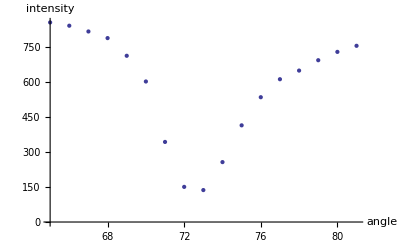

```mathematica
Show[ListPlot[data],AxesLabel-> {"angle","intensity"}]
```

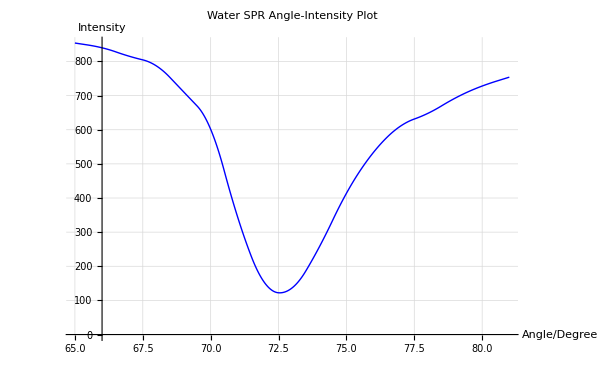

```mathematica
gra=ListLinePlot[data,Joined-> True,InterpolationOrder->2,PlotStyle->Blue,AxesLabel->{"Angle/Degree","Intensity"},PlotLabel->"Water SPR Angle-Intensity Plot",GridLines->Automatic]
```